# Symbolic Quantum Optimization for Interdisciplinary Learners

## Sebastián Rodríguez-Falcón Wolfram Research South America

## Open Quantum Institute - Quantum Hackaton LATAM 2025

## Max-Cut Problem

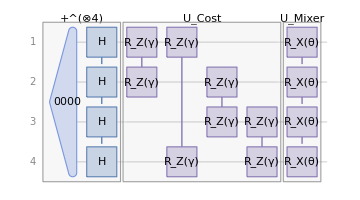
```mathematica
Grid[{{Text@Classical Formulation,Text@Quantum Formulation},{HoldForm[-Graphics-],-Graphics-},{Style[C=1/2∑_(𝒾,𝒿 ∈ V) (1-Subscript[s, 𝒾] Subscript[s, 𝒿]), 
s∈{-1,+1},FontSize->20],Style[Subscript[H, C]=1/2∑_(𝒾,𝒿 ∈ V) (𝟙-Subscript[Z, 𝒾] Subscript[Z, 𝒿])  
Subscript[Z, i] Subscript[Z, j] Subscript[x, 0](…x)_n=(-1)^Subscript[x, i](-1)^Subscript[x, j] Subscript[x, 0](…x)_n,Subscript[x, i]∈{0,1} ,FontSize->20]},{-Graphics-,-Graphics-}},Frame->All]
```

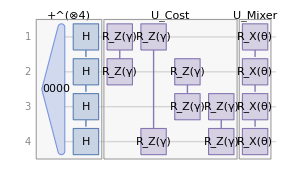
Classical Formulation | Quantum Formulation
-Graphics- | -Graphics-
C=1/2∑_(𝒾,𝒿 ∈ V) (1-s_𝒾 s_𝒿), 
s∈{-1,+1} | H_C=1/2∑_(𝒾,𝒿 ∈ V) (𝟙-Z_𝒾 Z_𝒿)  
Z_i Z_j x_0(…x)_n=(-1)^x_i(-1)^x_j x_0(…x)_n,x_i∈{0,1} 
-Graphics- | -Graphics-

## Understanding QAOA

Load Wolfram Quantum Framework

```mathematica
<<Wolfram`QuantumFramework`
```

Load Quantum Optimization Paclet

```mathematica
<<Wolfram`QuantumFramework`QuantumOptimization`
```

We are looking for “periodic” bitstrings:

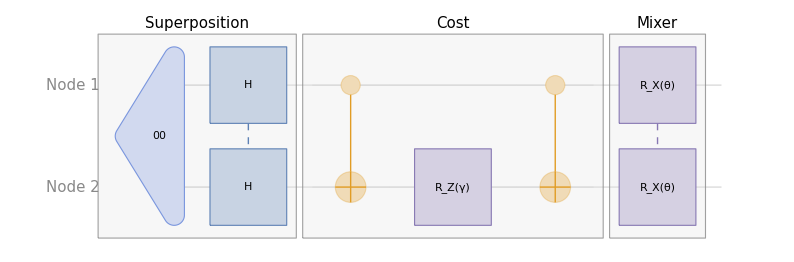

```mathematica
miniQAOA=;
miniQAOA["Diagram",]
```

Identifying a periodic and regular bitstring:

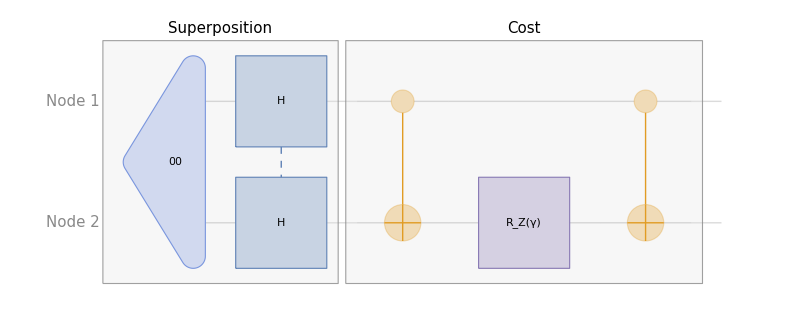

```mathematica
qc=miniQAOA[[;;2]];qc["Diagram",]
```

```mathematica
qc[]//TraditionalForm
```

1/2 ⅇ^(-(ⅈ γ)/2)00+1/2 ⅇ^((ⅈ γ)/2)01+1/2 ⅇ^((ⅈ γ)/2)10+1/2 ⅇ^(-(ⅈ γ)/2)11

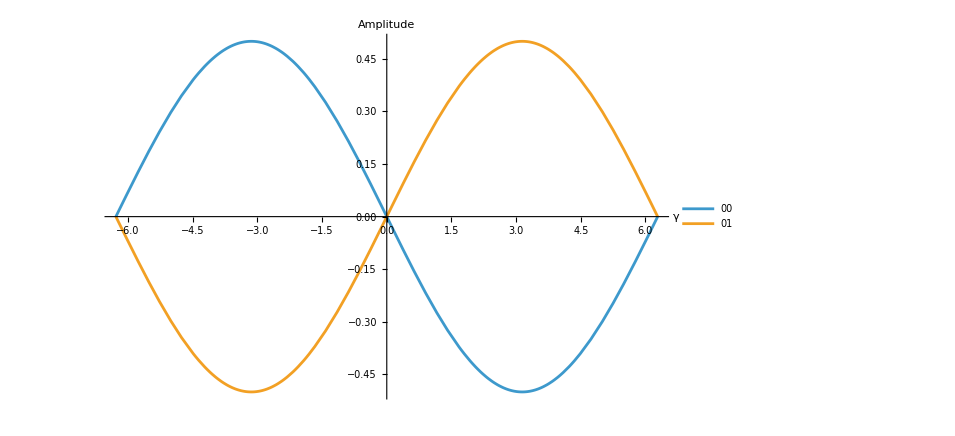

```mathematica
Plot[Evaluate[Im[Values[#1]]],{γ,-2 π,2 π},]&@qc["Amplitudes"][[;;2]]
```

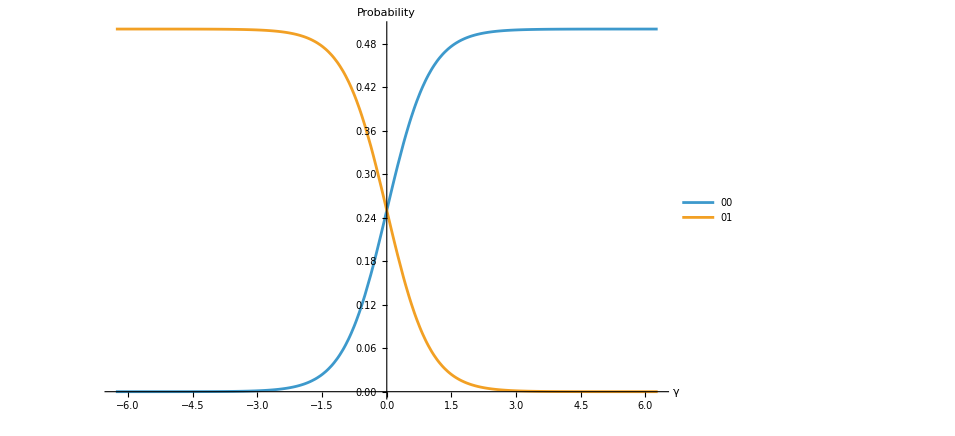

```mathematica
Plot[Evaluate[Values[#1]/.Im[γ]:>γ],{γ,-2 π,2 π},]&@qc["Probability"][[;;2]]
```

Mixing for every qubit:

```mathematica
miniQAOA["Simplify"]["Table"]
```

| 1
00 | ⅇ^(-(ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ]
01 | ⅇ^((ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
10 | ⅇ^((ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
11 | ⅇ^(-(ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ]

```mathematica
Plot3D[Evaluate[ComplexExpand@Values[#]],{γ,-2π,2π},{θ,-π,π},]&@miniQAOA[]["Probabilities"][[;;2]]
```

-Graphics3D-

## QAOA-in-QAOA

```mathematica
𝓍1=UndirectedEdge@@@{{1,2},{2,3},{3,4},{2,4},{1,3}};
𝓍2=UndirectedEdge@@@(4+{{1,2},{2,3},{3,4},{1,4},{2,4},{1,3}});
𝓍3=UndirectedEdge@@@(8+{{1,2},{2,3},{3,1}});
𝓍4=UndirectedEdge@@@(11+{{1,2}});
connection=UndirectedEdge@@@{{4,11},{10,7},{9,12},{13,5},{3,7},{1,8}};
edges={𝓍1,𝓍2,𝓍3,𝓍4};
fullEdges=Flatten[{{𝓍4,𝓍2,𝓍1,𝓍3},connection}];
subgraphs=Graph[#,EdgeWeight->Thread[Rule[#,1]],]&/@edges;
gsub=HighlightGraph[fullEdges,subgraphs,];
g13=Graph[fullEdges,PlotTheme->"NameLabeled",EdgeWeight->Thread[fullEdges->1]];
GraphicsRow[{g13,gsub},ImageSize->Full]
```

-Graphics-

## Divide Phase: Subgraphs

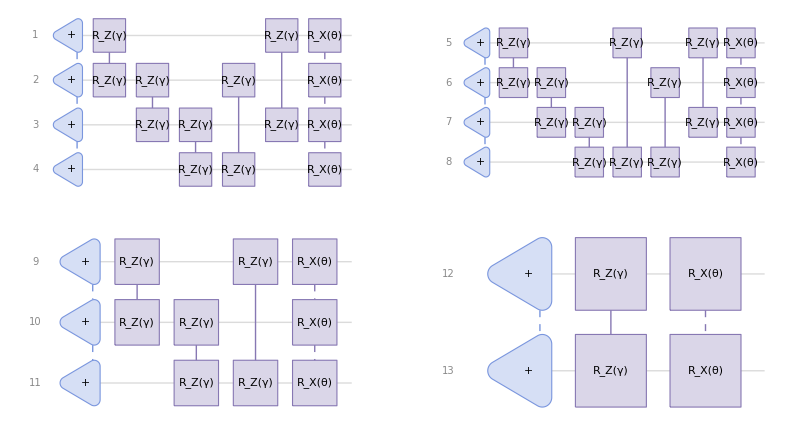

```mathematica
GraphicsGrid[Partition[#["Diagram","ShowEmptyWires"->False]&/@subQAOA,2],ImageSize->Full]
```

#### Cost Functions

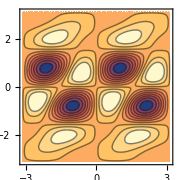
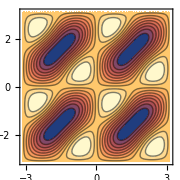
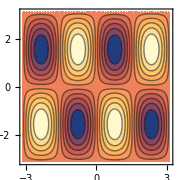
-Graphics- | -Graphics-
1/16 (-2 (3 sin(γ)+4 sin(2 γ)+3 sin(3 γ)) sin(2 θ)+4 cos(γ) (2 sin^2(γ) (cos(γ)+2) cos(2 θ)-1)+4 cos(3 γ)+cos(4 γ)+39) |  | -Graphics- | -Graphics-
3/8 (-8 sin(γ) cos^2(γ) sin(2 θ)+2 sin^2(2 γ) cos(2 θ)+cos(4 γ)+7) | 
-Graphics- | -Graphics-
3/8 (-2 sin(2 γ) sin(2 θ)+2 sin^2(γ) cos(2 θ)+cos(2 γ)+3) |  | -Graphics- | -Graphics-
1/2-sin(γ) sin(θ) cos(θ) |

```mathematica
sg=Subgraph[gsub,#,ImageSize->Small]&/@{Range[4],Range[5,8],{9,10,11},{12,13}};
minigrids=Grid[{{#[[1]],#[[2]]},{Text[#[[3]],FormatType->TraditionalForm],SpanFromLeft}},Frame->All,Background->{White,{None,Lighter[Yellow,.9]}},ItemStyle->#[[4]]]&/@Thread[{sg,contours,subcost,{8,12,12,12}}];
Grid[{#[[{1,2}]],#[[{3,4}]]}&@minigrids,Frame->All,BaselinePosition->Baseline,Alignment->Top,Background->Lighter[Blend[{Red,Lighter[Black,0.7]}],.3]]
```

#### Optimization

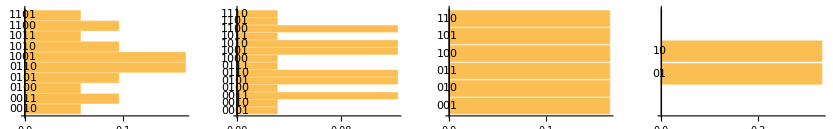

```mathematica
result=(#1⟦1⟧@@Values[Last[#1⟦2⟧]]&)/@Thread[{subQAOA,subres}];
GraphicsRow[#["ProbabilityPlot", ]&/@result]
```

```mathematica
states=Keys@ReverseSortBy[#["Probabilities"],#[[2]]]&/@result13;
groups=Map[states⟦Sequence@@##1⟧⟦1⟧&,{{1,2},{2,6},{3,1},{4,1}}];
solution=Flatten[Thread/@Thread[(First[#1["Order"]]&)/@subQAOA->groups]];
minig=Graph[g13,VertexLabels->MapAt[Placed[#1,Center]&,solution,{All,2}]];incompleteHigh=HighlightGraph[minig,(Subgraph[g13,#1]&)/@GatherBy[solution,Last]⟦All,All,1⟧,VertexLabelStyle->Directive[Black,12],GraphHighlightStyle->"Thick"];
GraphicsRow[{gsub,incompleteHigh},ImageSize->Full]
```

-Graphics-

## Conquer Phase: Big Graph

In the Conquer phase, we construct a new graph where each node represents a subgraph, and the edges are based on their prior connections:

```mathematica
as=<|solution|>;
bigEdges=Complement[EdgeList[g13],Flatten[EdgeList/@Map[Subgraph[g13,#]&,edges]]];
smallToBig=Flatten[Thread/@Thread[VertexList/@{𝓍1,𝓍2,𝓍3,𝓍4}->Range[4]]];
bigedges=EdgeList[bigEdges]/.z:UndirectedEdge[x_,y_]:>Rule[z/.smallToBig,(-1)^as[x]*(-1)^as[y]]//Merge[#,Total]&//Normal;
g2=Graph[Reverse@#[[All,1]],EdgeWeight->#,EdgeLabels->"EdgeWeight",EdgeLabelStyle->20,PlotTheme->"NameLabeled",VertexStyle->{1 -> Hue[0,0.57,0.78,0.4], 2 ->Hue[0.15,0.82,0.87,0.4],3->Hue[0.75,0.5,0.66,0.4],4->Hue[0.05,0.62,0.87,0.6]},ImageSize->Medium]&@bigedges;
ggg=Show[{Graphics[{
Hue[0.15,0.82,0.87,0.4],Disk[{1.7,0.5},0.8],
Hue[0,0.57,0.78,0.4],Disk[{0.45,1.8},{0.8,1}],
Hue[0.75,0.5,0.66,0.4],Disk[{2.43,2.5},0.75],
Hue[0.05,0.62,0.87,0.6],Disk[{3.65,1.4},{0.3,1}]
}],incompleteHigh
}];
GraphicsRow[{ggg,g2},ImageSize->10^2.9]
```

-Graphics-

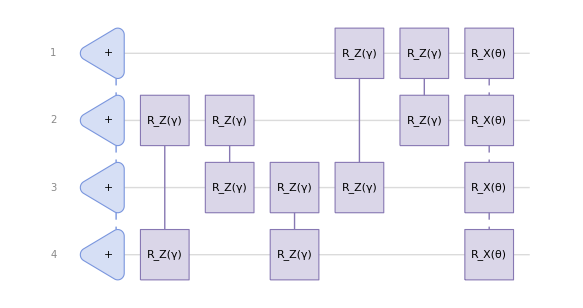

```mathematica
subQAOA2=QuantumCircuitOperator[{
"+"->VertexList[#1],
Sequence@@({"R",γ,"ZZ"}->#1&)/@List@@@EdgeList[#1],
"RX"[θ]->VertexList[#1]},
"Label"->None,"Parameters"->{θ,γ}]&@g2;
subQAOA2["Diagram"]
```

```mathematica
QAOAstates2=QuantumOperator[#]["State"]&@subQAOA2;
subcost2=("Scalar"//SuperDagger[QAOAstates2]@subHc2["State"]@QAOAstates2)//ComplexExpand//Simplify
```

1/32 (22-Cos[γ]+Cos[3 γ]+2 Cos[4 γ]-2 Cos[γ-2 θ]-3 Cos[3 γ-2 θ]-Cos[4 γ-2 θ]-Cos[2 (γ-θ)]+2 Cos[2 θ]+Cos[2 (γ+θ)]-Cos[2 (2 γ+θ)]+3 Cos[γ+2 θ]+2 Cos[3 γ+2 θ])

We observe the resulting probability distribution and solve the MaxCut problem for the higher-level graph:

```mathematica
result2=subQAOA2["State"][<| Last[NMaximize[subcost2,{θ,γ}]]|>];
```

```mathematica
probplot=result2["ProbabilityPlot", ];
```

```mathematica
groups2=Part[Keys@ReverseSortBy[#["Probabilities"],#[[2]]],2][[1]]&@result2;
solution2=Flatten[Thread/@Thread[First[#["Order"]]&@subQAOA2->groups2]];
grouped2=HighlightGraph[g2,Map[Subgraph[g13,#]&,GatherBy[solution2,Last][[All,All,1]]],];
GraphicsRow[{probplot,grouped2},ImageSize->Large]
```

-Graphics-

## Flipping & Correction

```mathematica
flip=Keys[Select[solution2,MatchQ[#,Rule[_,1]]&]];
newsolution=#->1-as[#]&/@Keys[Select[smallToBig,MatchQ[#,Rule[_,Alternatives@@flip]]&]];
finalsolution=Normal[Association[Join@@{solution,newsolution}]];
finalsol=HighlightGraph[g13,Map[Subgraph[g13,#]&,GatherBy[finalsolution,Last][[All,All,1]]],];
GraphicsRow[{incompleteHigh,Style["→",20],finalsol},ImageSize->Full]
```

-Graphics-

## Thanks!

Sebastián Rodríguez-Falcón

## References

“Quantum Optimization Tech Note”. Rodriguez, S. (2024). Wolfram Language Paclet Repository.
https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/tutorial/QuantumOptimization.html

“Symbolic methods in quantum optimization: introduction to QAOA-in-QAOA”. Rodriguez, S.​ (2025). Wolfram Community, STAFF PICKS.
https://community.wolfram.com/groups/-/m/t/3462606

“Exploring the quantum approximate optimization algorithm (QAOA) through the max-cut problem​”. Rodriguez, S. (2025). Wolfram Community, STAFF PICKS.
https://community.wolfram.com/groups/-/m/t/3449705

Zhou, Z., Du, Y., Tian, X., & Tao, D. (2023). QAOA-in-QAOA: Solving Large-Scale MaxCut Problems on Small Quantum Machines. Physical Review Applied, 19(2).
https://doi.org/10.1103/physrevapplied.19.024027

Esposito, A., & Danzig, T. (2024). Hybrid Classical-Quantum Simulation of MaxCut using QAOA-in-QAOA. In 2024 IEEE International Parallel and Distributed Processing Symposium Workshops (IPDPSW) (pp. 1088–1094).
https://doi.org/10.1109/ipdpsw63119.2024.00180

Blekos, K., Brand, D., Ceschini, A., Chou, C.-H., Li, R.-H., Pandya, K., & Summer, A. (2024). “A review on Quantum Approximate Optimization Algorithm and its variants”. Physics Reports (Vol. 1068, pp. 1–66).
https://doi.org/10.1016/j.physrep.2024.03.002

Ruslan Shaydulin (2021). Tutorial on Combinatorial Optimization on Quantum Computers. YouTube.
https://www.youtube.com/watch?v=5bSH1JIqyko

```mathematica
SetOptions[$FrontEndSession,AutoStyleOptions->{"UndefinedSymbolStyle"->{}}]
```